{structure}

{0,0,0,3}

{3.08203,2.96145,2.50016,2.04279}

{5.033,1.606,0.279,0}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}}

{physical quantity}

xi-Cos[xi] Sin[xi]

√(mi^2+xi^2/R^2)

(R (-3+2 mi R+4 R √(mi^2+xi^2/R^2)))/(6 (mi R+2 R √(mi^2+xi^2/R^2) (-1+R √(mi^2+xi^2/R^2))))

1+(-2 xi xj Sin[xi]^2 Sin[xj]^2-3/2 (xi-Cos[xi] Sin[xi]) (xj-Cos[xj] Sin[xj])+1/2 xi xj (2 xi SinIntegral[2 xi]-(xi-xj) SinIntegral[2 (xi-xj)]+2 xj SinIntegral[2 xj]-(xi+xj) SinIntegral[2 (xi+xj)]))/((xi Sin[xi]^2-3/2 (xi-Cos[xi] Sin[xi])) (xj Sin[xj]^2-3/2 (xj-Cos[xj] Sin[xj])))

{interaction energy}

0.296/Log[1+3.55872/R]

-1/(R^3 Log[1+3.55872/R])0.888 (0.+(0.0191959 R^2 (-3+8.17116 √(1/R^2) R)^2)/((-1+2.04279 √(1/R^2) R)^2)+(0. R (-3+0.558 R+4 √(0.077841+6.2508/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (0.279 R+2 √(0.077841+6.2508/R^2) R (-1+√(0.077841+6.2508/R^2) R)))+(0. R (-3+3.212 R+4 √(2.57924+8.77019/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (1.606 R+2 √(2.57924+8.77019/R^2) R (-1+√(2.57924+8.77019/R^2) R)))+(0. R (-3+10.066 R+4 √(25.3311+9.49891/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (5.033 R+2 √(25.3311+9.49891/R^2) R (-1+√(25.3311+9.49891/R^2) R))))

-1/R^31.65 (0.+(0.0191959 R^2 (-3+8.17116 √(1/R^2) R)^2)/((-1+2.04279 √(1/R^2) R)^2)+(0. R (-3+0.558 R+4 √(0.077841+6.2508/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (0.279 R+2 √(0.077841+6.2508/R^2) R (-1+√(0.077841+6.2508/R^2) R)))+(0. R (-3+3.212 R+4 √(2.57924+8.77019/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (1.606 R+2 √(2.57924+8.77019/R^2) R (-1+√(2.57924+8.77019/R^2) R)))+(0. R (-3+10.066 R+4 √(25.3311+9.49891/R^2) R) (-3+8.17116 √(1/R^2) R))/(√(1/R^2) (-1+2.04279 √(1/R^2) R) (5.033 R+2 √(25.3311+9.49891/R^2) R (-1+√(25.3311+9.49891/R^2) R))))

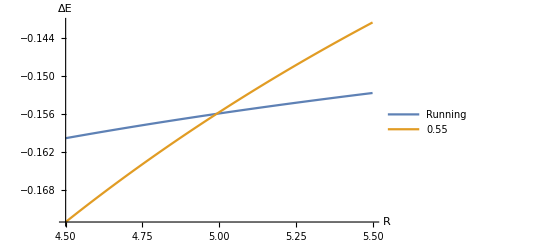

{integrate}

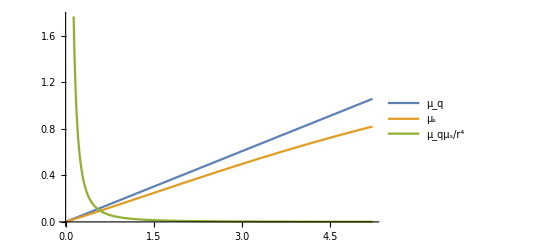

-0.154479

-0.16119

```mathematica
{"structure"}
n={0,0,0,3}
x={3.08203,2.96145,2.50016,2.04279}
m={5.033,1.606,0.279,0}
CMI={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,8}}

{"physical quantity"}
y[xi_]=xi-Sin[xi]Cos[xi]
ω[mi_,xi_,R_]=(mi^2+xi^2/R^2)^(1/2)
μ[mi_,xi_,R_]=R/6(4ω[mi,xi,R]R+2mi*R-3)/(2ω[mi,xi,R]R(ω[mi,xi,R]R-1)+mi*R)
Int[xi_,xj_,R_]=1+(xi*Sin[xi]^2-3/2 y[xi])^-1(xj*Sin[xj]^2-3/2 y[xj])^-1(-3/2 y[xi]*y[xj]-2xi*xj*Sin[xi]^2 Sin[xj]^2+1/2 xi*xj(2xi*SinIntegral[2xi]+2xj*SinIntegral[2xj]-(xi+xj)SinIntegral[2(xi+xj)]-(xi-xj)SinIntegral[2(xi-xj)]))

{"interaction energy"}
α[R_]=0.296/Log[1+1/(R*0.281)]
RunningΔEM[R_]=-3*α[R]/R^3*Sum[CMI[[p,q]]*μ[m[[p]],x[[p]],R]*μ[m[[q]],x[[q]],R]*Int[x[[p]],x[[q]],R],{p,1,4},{q,1,4}]
ΔEM[R_]=-3*0.55/R^3*Sum[CMI[[p,q]]*μ[m[[p]],x[[p]],R]*μ[m[[q]],x[[q]],R]*Int[x[[p]],x[[q]],R],{p,1,4},{q,1,4}]
Plot[{RunningΔEM[R],ΔEM[R]},{R,4.5,5.5},AxesLabel->{"R","ΔE"},PlotLegends->Placed[{"Running","0.55"},{0.7,0.8}]]

{"integrate"}
Plot[{μ[0,2.04,R],μ[0.279,2.45,R],μ[0,2.04,R]*μ[0.279,2.45,R]/R^4},{R,0,5.22},PlotLegends->Placed[{"μ_q","μ_s","μ_qμ_s/r^4"},{0.3,0.7}]]
RunningΔEM[5.22]
-3*α[5]/5^3*Sum[CMI[[p,q]]*μ[m[[p]],x[[p]],5]*μ[m[[q]],x[[q]],5]*(1+2NIntegrate[μ[0,2.04,R]*μ[0.279,2.45,R]/R^4,{R,0.025*5.22,5.22}]),{p,1,4},{q,1,4}]
```